```mathematica
ClearAll["Global`*"];Clear[Derivative];
T:=(2π)/ν;w:= (a Cos[ν t])/ν;LabelGr = {"q1", "q2","p1","p2"};
vec[x_]:=  {l[x] Sin[q[x, t]], w (2-x)+l[x]Cos[q[x,t]]}

r:= {vec [1], vec[1] + vec[2]}
dr:=D[r, t] /. Derivative[0,1][q][1,t]->dq1/.Derivative[0,1][q][2,t]-> dq2

L:=Sum[(m[i]dr[[i]].dr[[i]])/2+m[i]*g*r[[i]][[2]],{i,1,2}]

sol:=Solve[D[L,dq1]==p1&&D[L,dq2]==p2,{dq1,dq2}]
H:={dq1,dq2}.{p1,p2}-L/.sol[[1]]

{g, l[1], l[2], m[2], m[1]} = {1, 1, 1, 1, 1};
Hsub:= H/.q[1,t]->q1/.q[2,t]->q2//FullSimplify
HAver:=1/T Integrate[Hsub, {t, 0, T}]//FullSimplify
```

```mathematica
SubT[F_]:=F/.p1-> p1[t]/.p2-> p2[t]/.q1-> q1[t]/.q2-> q2[t]//FullSimplify
SolvDIff[F_, μ_:0]:=NDSolveValue[{
q1'[t]==D[F,p1[t]],
q2'[t]==D[F,p2[t]],
p1'[t]==-D[F,q1[t]]-μ q1'[t],
p2'[t]==-D[F,q2[t]]- μ (q2'[t] - q1'[t]),
q1[0]==z0[[1]],q2[0]==z0[[2]],p1[0]==z0[[3]],p2[0]==z0[[4]]
},
{q1,q2,p1,p2},
{t,0,end}]
Ploting[p_,style_]:= Plot[p,{t,0,end},PlotStyle->style]
ShowGraf[j_]:={
Ploting[solvH0[[j]][t],Blue],
Ploting[solvH1[[j]][t],Dashed],
Ploting[Abs[solvH1[[j]][t]-solvH0[[j]][t]],Red]
}
H0=SubT[Hsub];
H1 = SubT[HAver];
PlotAverAndFull[aa_, νν_, zz0_, eend_, μ_:0]:={
{a,ν,z0,end}= {aa,νν,zz0,eend};
solvH0= SolvDIff[H0, μ];
solvH1= SolvDIff[H1, μ];
Table[
Show[
ShowGraf[j][[1]],
ShowGraf[j][[2]], 
ShowGraf[j][[3]],
PlotLabel->LabelGr[[j]], 
PlotRange->All
],{j, 1,4}
]//Print;
}
```

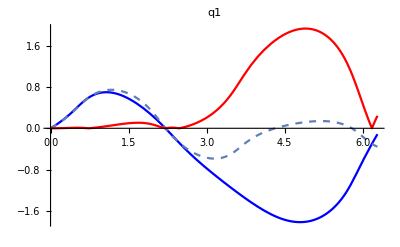
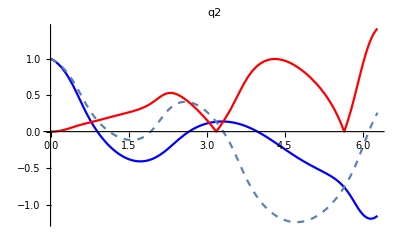
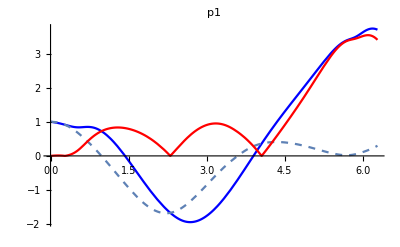
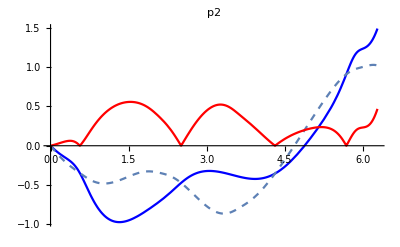

```mathematica
PlotAverAndFull[1,1,{0,1,1,0}, T];
```

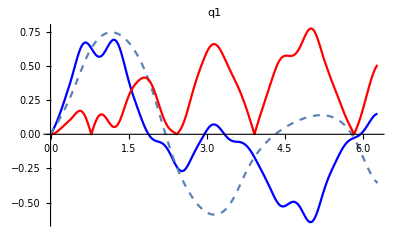
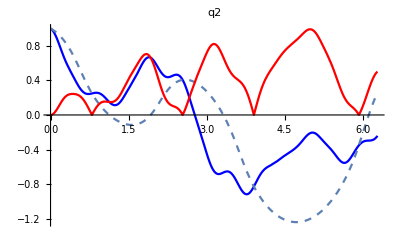
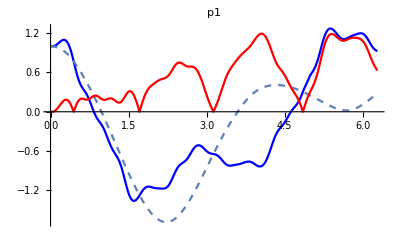
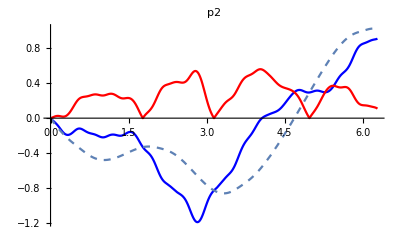

```mathematica
PlotAverAndFull[1,10,{0,1,1,0},T];
```

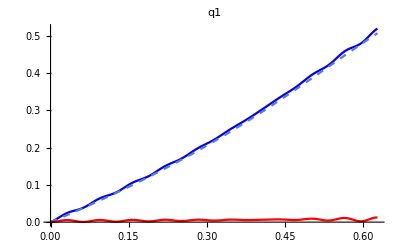
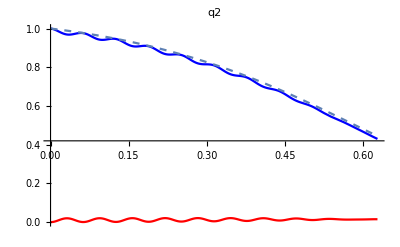
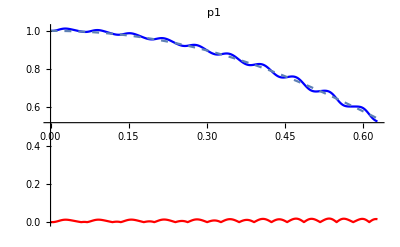
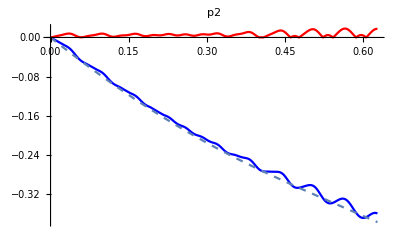

```mathematica
PlotAverAndFull[1,100,{0,1,1,0},T];
```

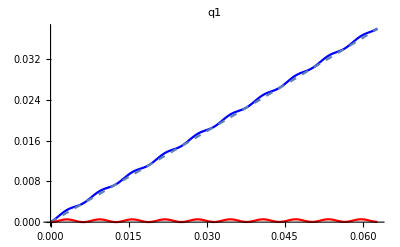
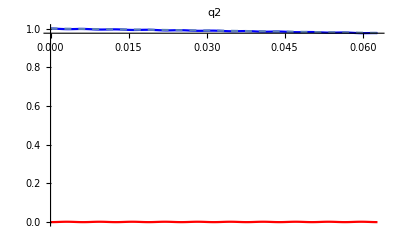
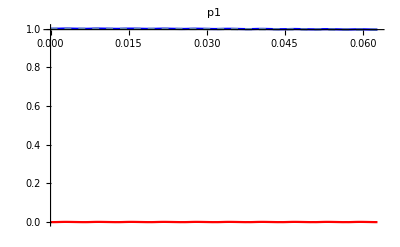
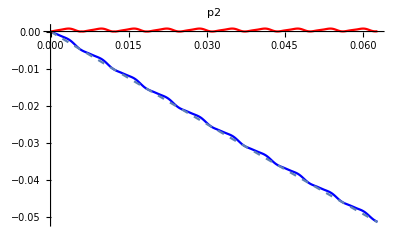

```mathematica
PlotAverAndFull[1,1000,{0,1,1,0},T];
```

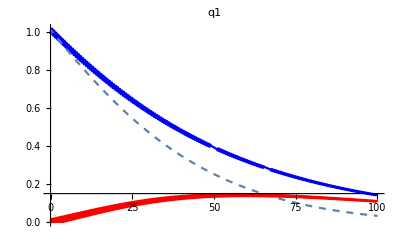
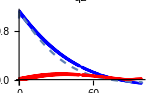
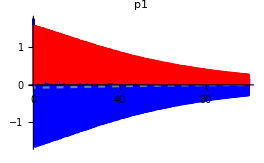
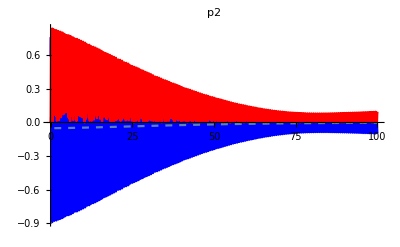

```mathematica
PlotAverAndFull[1,10,{1,1,1,10},100, 100];(*mu=100*)
```

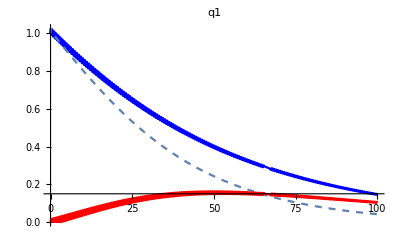
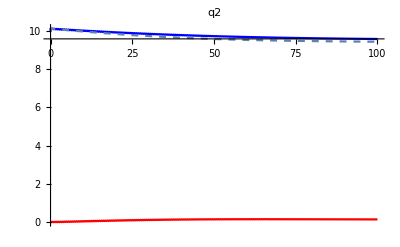
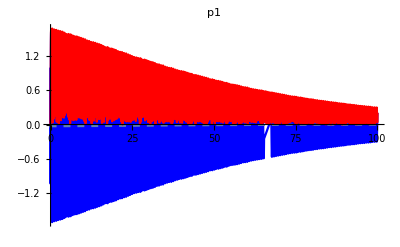
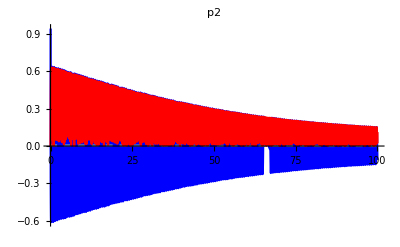

```mathematica
PlotAverAndFull[1,10,{1,10,1,10},100, 100];(*mu=100*)
```

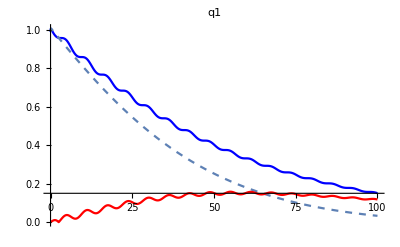
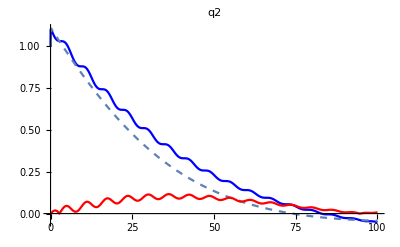
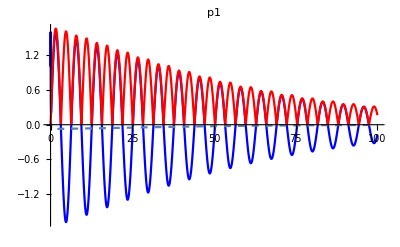
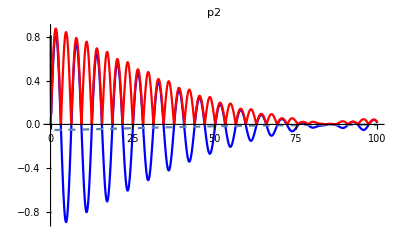

```mathematica
PlotAverAndFull[1,1,{1,1,1,10},100, 100];(*mu=100*)
```

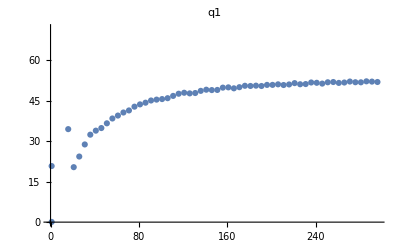
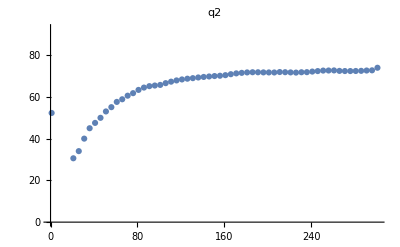
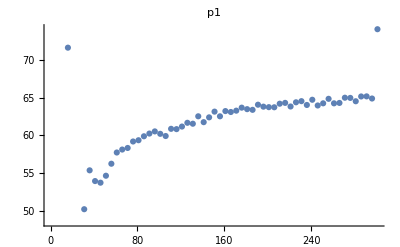
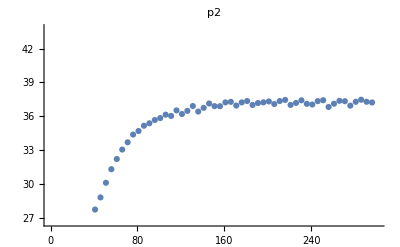

```mathematica
{a, ν,z0, end}={1,1,{0,1,1,0},100};
SolH0=SolvDIff[H0,10];
SolH1=SolvDIff[H1,10];
max=0;
Table[
Sol0=SolH0[[j]];
Sol1=SolH1[[j]];
For[τ=0,τ<end,τ=τ+0.05,If[max<Abs[Sol0[τ]-Sol1[τ]],max=Abs[Sol0[τ]-Sol1[τ]]]];
MAX2={{ν,max ν}};
For[ν=1,ν≤300,ν+=5,
SolH0=SolvDIff[H0];
SolH1=SolvDIff[H1];
max=0;
Sol0=SolH0[[j]];
Sol1=SolH1[[j]];
For[τ=0,τ<end,τ=τ+0.05,If[max<Abs[Sol0[τ]-Sol1[τ]],max=Abs[Sol0[τ]-Sol1[τ]]]];
MAX2=Append[MAX2,{ν,ν max}]
];
ListPlot[MAX2,PlotLabel-> LabelGr[[j]]],{j,1,4}]//Print;
```

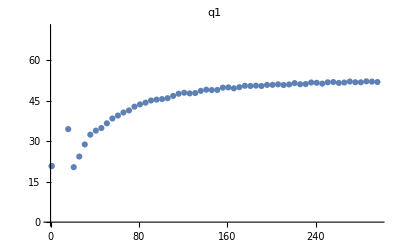
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{a, ν,z0, end}={1,1,{0,1,1,0},100};
SolH0=SolvDIff[H0];
SolH1=SolvDIff[H1];
max=0;
Table[
Sol0=SolH0[[j]];
Sol1=SolH1[[j]];
For[τ=0,τ<end,τ=τ+0.05,If[max<Abs[Sol0[τ]-Sol1[τ]],max=Abs[Sol0[τ]-Sol1[τ]]]];
MAX2={{ν,max ν}};
For[ν=1,ν≤300,ν+=5,
SolH0=SolvDIff[H0];
SolH1=SolvDIff[H1];
max=0;
Sol0=SolH0[[j]];
Sol1=SolH1[[j]];
For[τ=0,τ<end,τ=τ+0.05,If[max<Abs[Sol0[τ]-Sol1[τ]],max=Abs[Sol0[τ]-Sol1[τ]]]];
MAX2=Append[MAX2,{ν,ν max}]
];
ListPlot[MAX2,PlotLabel-> LabelGr[[j]]],{j,1,4}]//Print;
```

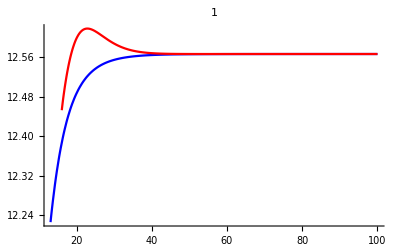

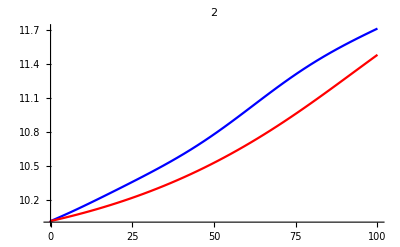

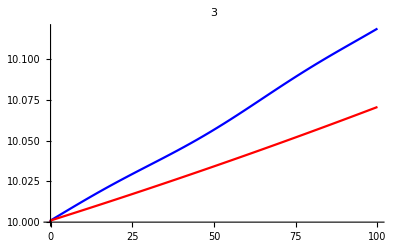

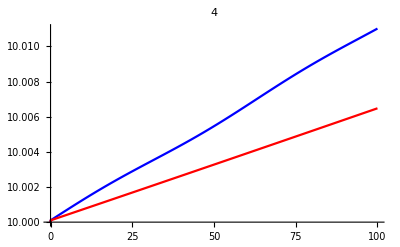

```mathematica
{a,ν,z0,end}= {1,0.1,{10,10,1,1},100};
For[j=1,j<=4,j++,
SolvD=SolvDIff[H0,10^j];
SolvDMu=SolvDIff[H1,10^j];
gr=Plot[SolvD[[1]][t],{t,0,end},PlotStyle->Blue];
grMu=Plot[SolvDMu[[1]][t],{t,0,end},PlotStyle->Red];
Show[gr,grMu,PlotLabel->j, PlotRange->All]//Print]
```

```mathematica
{a,ν,z0,end}= {1,100,{0,0,1,1},10};
solvH1= SolvDIff[H1, 1];
Ploting[solvH1[[1]][t],Blue]
```

```mathematica
{a,ν,z0,end}= {1,100,{0,0,1,1},T};
solvH1= SolvDIff[H1, 0];
Ploting[solvH1[[1]][t],Blue]
```